```mathematica
Clear["Global`*"]
```

```mathematica
LaunchKernels[]
```

$Failed

```mathematica
(*Константы*)
```

```mathematica
Ung=200*10^9;
ν=0.3;
DD={{λ+2*μ,λ,0},{λ,λ+2μ,0},{0,0,μ}};
λ=ν*Ung/(1+ν)/(1-2*ν);
μ=Ung/2/(1+ν);
ρ=7850;
MatrixForm@DD;
ϵ0={{α*dt},{α*dt},{0}};
α=13*10^-15;
dt=10;
ROpt=1;
a=0.5;
a1=2;
a2=3;
Reg1=Parallelogram[{0,0},{{0,a1},{a2,0}}];
(*Reg5=Disk[{3a,2a},a/2];*)
Reg1234=RegionUnion[Reg1];
(*ℛ=RegionDifference[Reg1234,Reg5];*)
Reg=DiscretizeRegion[Reg1234,MeshCellLabel->{0->"Index"},MaxCellMeasure->.01];
Coord=MeshCoordinates[Reg];
Polys=MeshCells[Reg,2];
ActionSquare=Show[Reg,ImageSize->600];
```

#### Инициализация

```mathematica
Emin=2*10^5;
E0=Ung;
DP=3;
ñ=0.05;
m=ROpt*10^(-4);
RhoMin=ROpt*10^(-1);
SquareS=Table[S[i],{i,1,Length@Polys}];
Rmin=REQ=Sqrt[Max@SquareS/Pi]*4;
For[i=1,i≤Length[Polys],i++,rho[i]=1];
OptimizationCode=0;
Width=Table[rho[i],{i,1,Length[Polys]}];
S[i_]:=0.5*((Coord[[Polys[[i,1,1]],1]]-Coord[[Polys[[i,1,3]],1]])*(Coord[[Polys[[i,1,2]],2]]-Coord[[Polys[[i,1,3]],2]])-(Coord[[Polys[[i,1,2]],1]]-Coord[[Polys[[i,1,3]],1]])*(Coord[[Polys[[i,1,1]],2]]-Coord[[Polys[[i,1,3]],2]]));
ai[i_]:=Coord[[Polys[[i,1,2]],1]]*Coord[[Polys[[i,1,3]],2]]-Coord[[Polys[[i,1,3]],1]]*Coord[[Polys[[i,1,2]],2]];
bi[i_]:=Coord[[Polys[[i,1,2]],2]]-Coord[[Polys[[i,1,3]],2]];
ci[i_]:=Coord[[Polys[[i,1,3]],1]]-Coord[[Polys[[i,1,2]],1]];
(*j*)
aj[i_]:=Coord[[Polys[[i,1,3]],1]]*Coord[[Polys[[i,1,1]],2]]-Coord[[Polys[[i,1,1]],1]]*Coord[[Polys[[i,1,3]],2]];
bj[i_]:=Coord[[Polys[[i,1,3]],2]]-Coord[[Polys[[i,1,1]],2]];
cj[i_]:=Coord[[Polys[[i,1,1]],1]]-Coord[[Polys[[i,1,3]],1]];
(*m*)
am[i_]:=Coord[[Polys[[i,1,1]],1]]*Coord[[Polys[[i,1,2]],2]]-Coord[[Polys[[i,1,2]],1]]*Coord[[Polys[[i,1,1]],2]];
bm[i_]:=Coord[[Polys[[i,1,1]],2]]-Coord[[Polys[[i,1,2]],2]];
cm[i_]:=Coord[[Polys[[i,1,2]],1]]-Coord[[Polys[[i,1,1]],1]];
(*Функции формы*)
Ni[i_]:=1/(2S[i])*(ai[i]+bi[i]*x+ci[i]*y);
Nj[i_]:=1/(2S[i])*(aj[i]+bj[i]*x+cj[i]*y);
Nm[i_]:=1/(2S[i])*(am[i]+bm[i]*x+cm[i]*y);
ϝ[b_]:={{DS[[NUM[b][[1]]]]},{DS[[NUM[b][[2]]]]},{DS[[NUM[b][[3]]]]},{DS[[NUM[b][[4]]]]},{DS[[NUM[b][[5]]]]},{DS[[NUM[b][[6]]]]}};
PreIntB[i_]:=Transpose[B[[i]]].DD.B[[i]];
NUM[i_]:={Polys[[i,1,1]]*2-1,Polys[[i,1,1]]*2,Polys[[i,1,2]]*2-1,Polys[[i,1,2]]*2,Polys[[i,1,3]]*2-1,Polys[[i,1,3]]*2};
Ke[i_]:=PreIntB[i]*S[i]*Width[[i]];
XC[i_]:=(Coord[[Polys[[i,1,1]],1]]+Coord[[Polys[[i,1,2]],1]]+Coord[[Polys[[i,1,3]],1]])/3;
YC[i_]:=(Coord[[Polys[[i,1,1]],2]]+Coord[[Polys[[i,1,2]],2]]+Coord[[Polys[[i,1,3]],2]])/3;
EE[i_]:=Emin+(rho[i]/ROpt)^DP*(E0-Emin);
ϝ[b_]:={{DS[[NUM[b][[1]]]]},{DS[[NUM[b][[2]]]]},{DS[[NUM[b][[3]]]]},{DS[[NUM[b][[4]]]]},{DS[[NUM[b][[5]]]]},{DS[[NUM[b][[6]]]]}};
BB[i_]:=DP*rho[i]^(DP-1)*Transpose[ϝ[i]].LocalKE[[i]].ϝ[i];
TimeObject[Now]
B=ParallelTable[{
{D[Ni[i],x],0,D[Nj[i],x],0,D[Nm[i],x],0},
{0,D[Ni[i],y],0,D[D[Nj[i],y]],0,D[D[Nm[i],y]]},
{D[Ni[i],y],D[Ni[i],x],D[Nj[i],y],D[Nj[i],x],D[Nm[i],y],D[Nm[i],x]}
},{i,1,Length@Polys}];
ℋ=ParallelTable[If[Rmin-Sqrt[(XC[i]-XC[j])^2+(YC[i]-YC[j])^2]>0,Rmin-Sqrt[(XC[i]-XC[j])^2+(YC[i]-YC[j])^2],0],{i,1,Length@Polys},{j,1,Length@Polys}];
TimeObject[Now]
```

14:10:25GMT-7.TimeObject[{14,10,25.1947},TimeZone→-7.]

14:10:33GMT-7.TimeObject[{14,10,33.7718},TimeZone→-7.]

```mathematica
OP=0;
DSC={};
(*NumberOFPoints1=Table["N1="<>ToString[i]:>(N1=i;),{i,1,Length@Coord}];
NumberOFPoints2=Table["N2="<>ToString[i]:>(N2=i;),{i,1,Length@Coord}];*)
(*ButtonN1=ActionMenu["Choose N1",NumberOFPoints1]
ButtonN2=ActionMenu["Choose N2",NumberOFPoints2]*)
ButtonK1=Control[{k1,Table[i,{i,1,Length@Coord}]}];
ButtonK2=Control[{k2,Table[i,{i,1,Length@Coord}]}];
ButtonN1=Control[{N1,Table[i,{i,1,Length@Coord}]}];
ButtonN2=Control[{N2,Table[i,{i,1,Length@Coord}]}];
ButtonRhoMax=Control[{RhoMax,Table[N[50/i],{i,1,100}]}];
ButtonMassCoeff=Control[{MassCoeff,Table[N[10/i],{i,1,20}]}];
ButtonReper=Control[{Reper,Table[i,{i,1,Length@Coord}]}];
(*ButtonRadius=Control[{Rmin,Table[i*REQ,{i,1,16}]}];*)
ButtonLegrange=Control[{λegrange,Table[i,{i,1,2500}]}];
ButtonClearingResults=Button["ClearResults",For[i=1,i≤Length[Polys],i++,rho[i]=1]; OptimizationCode=0;OP=0;DSC={};];
ButtonOpt=Button["Optimize",
Width=Table[rho[i],{i,1,Length[Polys]}];
OP=OP+1;
LocalKE=Table[Ke[i],{i,1,Length[Polys]}];
StifnessMatrix=Table[0,{i,1,Length[Coord]*2},{j,1,Length[Coord]*2}];
For[b=1,b≤Length[Polys],b++,
For[p=1,p<=6,p++,
For[g=1,g<=6,g++,
StifnessMatrix[[NUM[b][[p]],NUM[b][[g]]]]=LocalKE[[b,p,g]]+StifnessMatrix[[NUM[b][[p]],NUM[b][[g]]]];
];
];
];
(*==========================================================================*)
(*Формирование силовых факторов и перемещений*)
Displacement=Table[δ[i],{i,1,Length[Coord]*2}];
Force=Table[f[i],{i,1,Length[Coord]*2}];
(*==========================================================================*)
(*Сосредоточенная нагрузка*)
(*k1=1;
k2=53;*)
For[i=1,i≤Length[Coord]*2,i++,
f[i]=0;
];
f[k1*2]=-100000*9.8;
f[k2*2]=-100000*9.8*0;
(*==========================================================================*)
(*Распределенные нагрузки*)
(*==========================================================================*)
(*N1=70;
N2=69;
Q=-500000*0;
L=2;
Incr=0;
For[b=1,b≤Length[Coord],b++,
If[Coord[[b,L]]==Coord[[N1,L]],Incr=Incr+1]
];
FPress=Q*Abs[(Coord[[N1,1]]-Coord[[N2,1]])]*Width[[1]];*)
(*==========================================================================*)
(*For[b=1,b≤Length[Coord],b++,
If[Coord[[b,L]]==Coord[[N1,L]],f[2*b-1]=f[2*b-1]+FPress/Incr]
];*)
(*==========================================================================*)
(*Формирование СЛАУ*)
J=1;(*Номер компоненты*)
H=a2;(*Величина компоненты на границе*)
Equation={};
(*==========================================================================*)
For[i=1,i≤Length[Coord],i++,
If[Coord[[i,J]]≠H(*&&Coord[[i,J]]≠0,*),
Equation=Append[Equation,StifnessMatrix[[2i-1]].Displacement==f[2i-1]];
Equation=Append[Equation,StifnessMatrix[[2i]].Displacement==f[2i]];
];
];
(*==========================================================================*)
For[i=1,i≤Length[Coord],i++,
If[Coord[[i,J]]==H,
δ[2*i-1]=0;
δ[2*i]=0
];
(*If[Coord[[i,J]]==0,
δ[2*i-1]=0;
δ[2*i]=0
];*)
];
(*==========================================================================*)
DisplacementI={};
(*==========================================================================*)
For[i=1,i≤Length[Coord]*2,i++,
If[δ[i]≠0,DisplacementI=Append[DisplacementI,δ[i]]];
];
(*==========================================================================*)
Sols=NSolve[Equation,DisplacementI];
DS=Displacement/.Sols[[1]];
CoordDeformed={};
CoordUndeformed={};
If[OptimizationCode==0,InitialDisplacement=DS;
DSC=Append[DSC,
Table[
N@Sqrt[DS[[i*2-1]]^2+DS[[i*2]]^2],
{i,1,Length@Coord}]];
];
If[OptimizationCode≠0,ODisplacement=DS;
DSC=Append[DSC,
Table[
N@Sqrt[DS[[i*2-1]]^2+DS[[i*2]]^2],
{i,1,Length@Coord}]];
];
(*==========================================================================*)
For[i=1,i≤Length[Coord],i++,
CoordDeformed=Append[CoordDeformed,{Coord[[i,1]]+DS[[2i-1]],Coord[[i,2]]+DS[[2i]]}];
CoordUndeformed=Append[CoordUndeformed,{Coord[[i,1]],Coord[[i,2]]}];
];
(*==========================================================================*)
(*Обратный ход для получения напряжений*)
For[b=1,b≤Length[Polys],b++,
ϵe[b]=B[b].ϝ[b];
σ[b]=DD.ϵe[b];
];
(*==========================================================================*)
(*Оптимизация формы*)
(*==========================================================================*)
DecreaseB=Table[BB[i][[1]],{i,1,Length[Polys]}]/(*λegrange*)Max[Table[BB[i][[1]],{i,1,Length[Polys]}]]/(3*OP)^(1/3);(*==========================================================================*)
For[i=1,i≤Length[Polys],i++,
If[Max[rho[i]-m,RhoMin]>rho[i]*DecreaseB[[i,1]]^ñ,
rho[i]=Max[rho[i]-m,RhoMin]
];
If[Min[rho[i]+m,RhoMax]<rho[i]*DecreaseB[[i,1]]^ñ,
rho[i]=Min[rho[i]+m,RhoMax],
rho[i]=rho[i]*DecreaseB[[i,1]]^ñ
];
];
(*==========================================================================*)
(*Выравнивание массы всех элементов*)
For[i=1,i<=Length[Polys],i++,If[rho[i]<RhoMin,rho[i]=RhoMin]];
For[i=1,i<=Length[Polys],i++,If[rho[i]>RhoMax,rho[i]=RhoMax]];
V1=Sum[rho[i]*S[i],{i,1,Length[Polys]}];
V2=Sum[S[i]*ROpt,{i,1,Length[Polys]}];
For[i=1,i≤Length[Polys],i++,rho[i]=rho[i]*V2/V1*MassCoeff];
WD=Table[rho[i],{i,1,Length[Polys]}];
(*==========================================================================*)
Graph2D={};
For[v=1,v≤Length@Polys,v++,
If[WD[[v]]>0.5,
Graph2D=Append[Graph2D,
{EdgeForm[Black],Gray,Opacity[WD[[v]]],
Polygon[{
{CoordUndeformed[[Polys[[v,1,1]]]][[1]],CoordUndeformed[[Polys[[v,1,1]]]][[2]]},{CoordUndeformed[[Polys[[v,1,2]]]][[1]],CoordUndeformed[[Polys[[v,1,2]]]][[2]]},{CoordUndeformed[[Polys[[v,1,3]]]][[1]],CoordUndeformed[[Polys[[v,1,3]]]][[2]]}
}]}]
];
];
G4=Graphics[Graph2D];
(*==========================================================================*)
Graph3DNotOpt={};
For[v=1,v≤Length@Polys,v++,
If[rho[v]>0.5,
Graph3DNotOpt=Append[Graph3DNotOpt,
{EdgeForm[Thickness[0]],GrayLevel[WD[[v]]],Opacity[WD[[v]]],
Prism[{
{CoordUndeformed[[Polys[[v,1,1]]]][[1]],CoordUndeformed[[Polys[[v,1,1]]]][[2]],rho[v]^0.5/2/2},{CoordUndeformed[[Polys[[v,1,2]]]][[1]],CoordUndeformed[[Polys[[v,1,2]]]][[2]],rho[v]^0.5/2/2},{CoordUndeformed[[Polys[[v,1,3]]]][[1]],CoordUndeformed[[Polys[[v,1,3]]]][[2]],rho[v]^0.5/2/2},
{CoordUndeformed[[Polys[[v,1,1]]]][[1]],CoordUndeformed[[Polys[[v,1,1]]]][[2]],-rho[v]^0.5/2/2},{CoordUndeformed[[Polys[[v,1,2]]]][[1]],CoordUndeformed[[Polys[[v,1,2]]]][[2]],-rho[v]^0.5/2/2},{CoordUndeformed[[Polys[[v,1,3]]]][[1]],CoordUndeformed[[Polys[[v,1,3]]]][[2]],-rho[v]^0.5/2/2}
}]}]
];
];
G3NO=
Graphics3D[Graph3DNotOpt,ViewPoint->{-1,-2,2},ImageSize->600];
(*==========================================================================*)
Beep[];
OptimizationCode=OptimizationCode*10+1;
];
ButtonCheck=Button["Remove CheckerBoard",
(*==========================================================================*)
(*Вектор H, удаление проблемы шахматной доски.*)
OP=0;
ℛ=ParallelTable[(1/Sum[ℋ[[i,j]],{j,1,Length[Polys]}])*Sum[ℋ[[i,j]]*rho[j]*DP*rho[j]^(DP-1)*Transpose[ϝ[j]].LocalKE[[j]].ϝ[j],{j,1,Length[Polys]}],{i,1,Length@Polys}];FilterMatrix=ParallelTable[ℛ[[i,1,1]],{i,1,Length[Polys]}];
Beep[];
(*==========================================================================*)
V1R=Sum[FilterMatrix[[i]]*S[i],{i,1,Length[Polys]}];
FilterMatrixDensity=FilterMatrix*V2/V1R*MassCoeff;
For[i=1,i≤Length@Polys,i++,
rho[i]=FilterMatrixDensity[[i]]
];
Graph3DOpt={};
For[v=1,v≤Length@Polys,v++,
If[rho[v]>0.5,
Graph3DOpt=Append[Graph3DOpt,
{EdgeForm[Thickness[0]],GrayLevel[rho[v]],Opacity[rho[v]],
Prism[{
{CoordUndeformed[[Polys[[v,1,1]]]][[1]],CoordUndeformed[[Polys[[v,1,1]]]][[2]],rho[v]^0.5/2/2},{CoordUndeformed[[Polys[[v,1,2]]]][[1]],CoordUndeformed[[Polys[[v,1,2]]]][[2]],rho[v]^0.5/2/2},{CoordUndeformed[[Polys[[v,1,3]]]][[1]],CoordUndeformed[[Polys[[v,1,3]]]][[2]],rho[v]^0.5/2/2},
{CoordUndeformed[[Polys[[v,1,1]]]][[1]],CoordUndeformed[[Polys[[v,1,1]]]][[2]],-rho[v]^0.5/2/2},{CoordUndeformed[[Polys[[v,1,2]]]][[1]],CoordUndeformed[[Polys[[v,1,2]]]][[2]],-rho[v]^0.5/2/2},{CoordUndeformed[[Polys[[v,1,3]]]][[1]],CoordUndeformed[[Polys[[v,1,3]]]][[2]],-rho[v]^0.5/2/2}
}]}]
];
];
G3VD=Graphics3D[Graph3DOpt,ViewPoint->{-1,-2,2},ImageSize->600];
OptimizationCode=OptimizationCode*10+2;
];
```

```mathematica
Buttons=Grid[{{"K1","K2","ReperPoint"},{ButtonK1,ButtonK2,ButtonReper},{"N1","N2","DisplacementChange"},{ButtonN1,ButtonN2,Dynamic[N@Sqrt[ODisplacement[[Reper*2-1]]^2+ODisplacement[[Reper*2]]^2]/N@Sqrt[InitialDisplacement[[Reper*2-1]]^2+InitialDisplacement[[Reper*2]]^2]*100]},{ButtonClearingResults,"λ","OptimizationCode"},{"_",ButtonLegrange,Dynamic@OptimizationCode},{"RhoMax","MassCoeff"},{ButtonRhoMax,ButtonMassCoeff}},Frame->All];
Grid[{{ActionSquare,Buttons},{ButtonOpt,ButtonCheck},{Dynamic@Show[G3NO],Dynamic@Show[G3VD]}},Frame->All]
```

-Graphics- | K1 | K2 | ReperPoint
 |  | 
N1 | N2 | DisplacementChange
 |  | 
ClearResults | λ | OptimizationCode
_ |  | 
RhoMax | MassCoeff | 
 |  | 
Optimize | Remove CheckerBoard
 |

```mathematica
Dynamic[Max@WD]
Dynamic[Min@WD]
```

```mathematica
Results=Grid[{{ActionSquare,Buttons},{ButtonOpt,ButtonCheck},{Dynamic@Show[G3NO],Dynamic@Show[G3VD]}},Frame->All];
Export["E:\\TopologyOpt\\"<>ToString[λegrange]<>"FF"<>ToString[OptimizationCode]<>".png",Results]
```

E:\TopologyOpt\50FF11111111112.png

```mathematica
(*Points={};*)
```

```mathematica
Points=Append[Points,DSC];
```

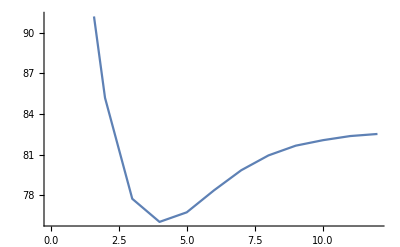

```mathematica
RR=72;
ListLinePlot[Table[DSC[[i,RR]]/DSC[[1,RR]]*100,{i,1,Length@DSC}]]
```

```mathematica
DSC[[12,RR]]/DSC[[1,RR]]
```

0.825318

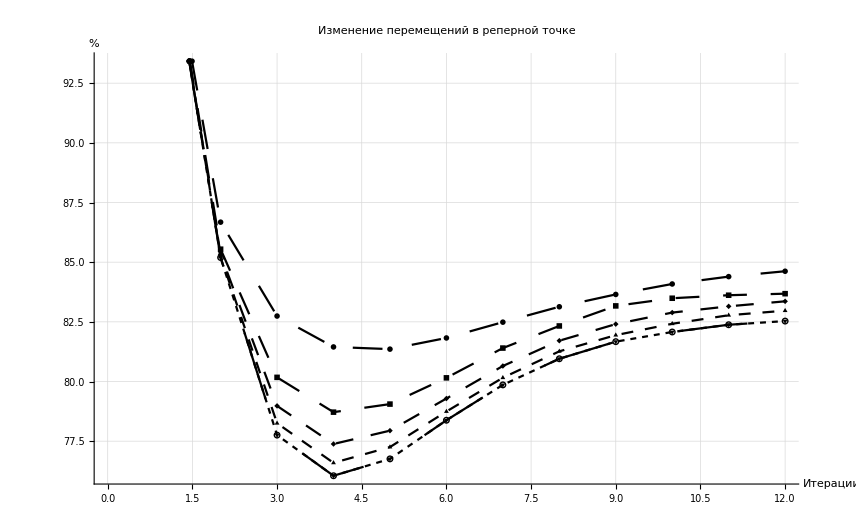

```mathematica
RR=72;
ListLinePlot[Table[Table[Points[[j,i,RR]]/Points[[j,1,RR]]*100,{i,1,Length@DSC}],{j,1,Length@Points}],AxesLabel->{Style["Итерации",20,Black],Style["%",20,Black]},AxesStyle->Directive[Black,16],PlotLabel->Style["Изменение перемещений в реперной точке",20,Black],PlotStyle->{{Black,Dashing[0.025]},{Black,Dashing[0.020]},{Black,Dashing[0.015]},{Black,Dashing[0.010]},{Black,Dashing[0.005]},{Black,Dashing[0.1]}},PlotMarkers->{Automatic,Medium},GridLines->Automatic]
```

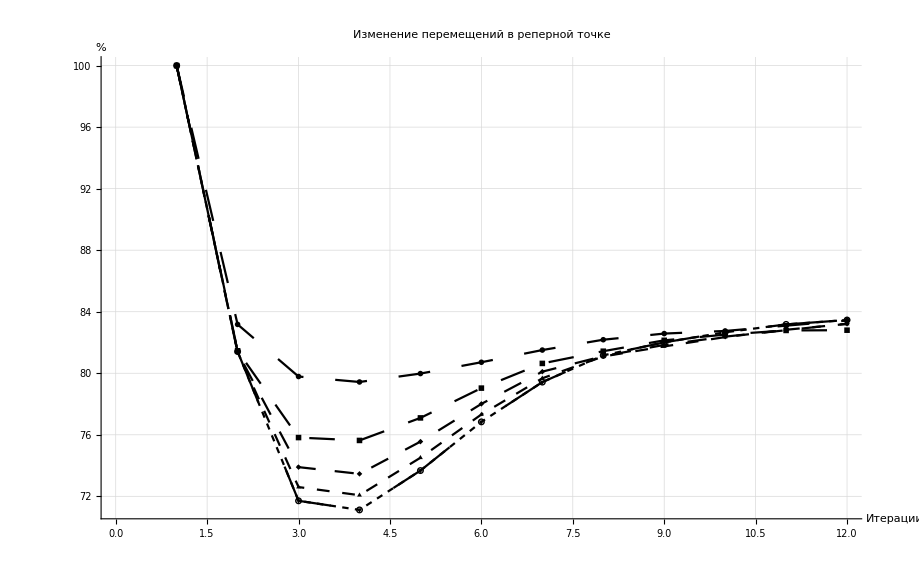

```mathematica
RR=164;
ListLinePlot[Table[Table[Points[[j,i,RR]]/Points[[j,1,RR]]*100,{i,1,Length@DSC}],{j,1,Length@Points}],AxesLabel->{Style["Итерации",20,Black],Style["%",20,Black]},AxesStyle->Directive[Black,16],PlotLabel->Style["Изменение перемещений в реперной точке",20,Black],PlotStyle->{{Black,Dashing[0.025]},{Black,Dashing[0.020]},{Black,Dashing[0.015]},{Black,Dashing[0.010]},{Black,Dashing[0.005]},{Black,Dashing[0.1]}},PlotMarkers->{Automatic,Medium},GridLines->Automatic]
```